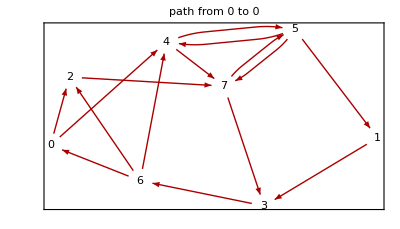

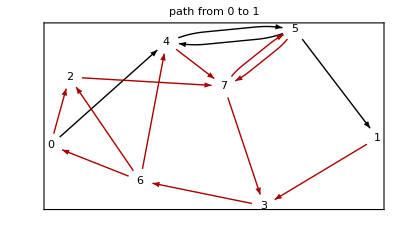

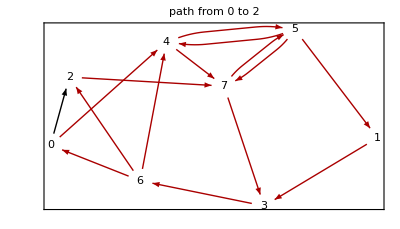

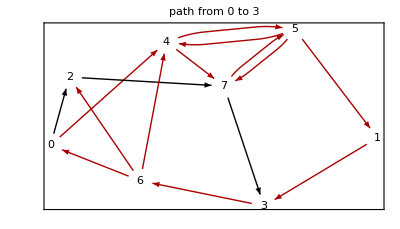

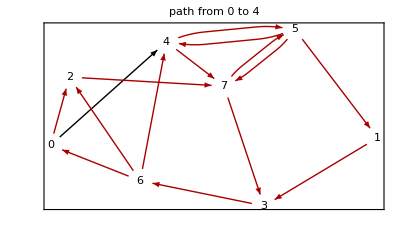

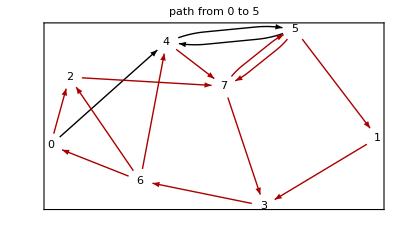

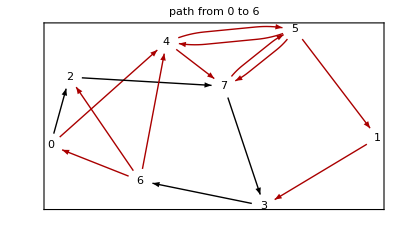

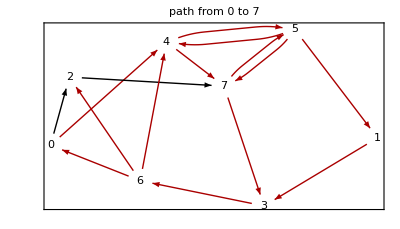

```mathematica
edges={4->5,5->4,4->7,5->7,7->5,5->1,0->4,0->2,7->3,1->3,2->7,6->2,3->6,6->0,6->4};
path={0};
edgesToHighlight=Partition[path,2,1];
edgesToHighlight=Join[edgesToHighlight,Reverse/@edgesToHighlight];
erf[pts_,edge_,___]:=If[MemberQ[edgesToHighlight,edge],{Thick,Black,{Arrowheads[Large],Arrow[pts,0.1]}},{Darker[Red],{Arrowheads[Medium],Arrow[pts,0.1]}}];
GraphPlot[edges,PlotLabel->"path from 0 to 0",DirectedEdges->True,VertexLabeling->True,Frame->True,EdgeRenderingFunction->erf,Method->"SpringEmbedding"]

edges={4->5,5->4,4->7,5->7,7->5,5->1,0->4,0->2,7->3,1->3,2->7,6->2,3->6,6->0,6->4};
path={0,4,5,1};
edgesToHighlight=Partition[path,2,1];
edgesToHighlight=Join[edgesToHighlight,Reverse/@edgesToHighlight];
erf[pts_,edge_,___]:=If[MemberQ[edgesToHighlight,edge],{Thick,Black,{Arrowheads[Large],Arrow[pts,0.1]}},{Darker[Red],{Arrowheads[Medium],Arrow[pts,0.1]}}];
GraphPlot[edges,PlotLabel->"path from 0 to 1",DirectedEdges->True,VertexLabeling->True,Frame->True,EdgeRenderingFunction->erf,Method->"SpringEmbedding"]

edges={4->5,5->4,4->7,5->7,7->5,5->1,0->4,0->2,7->3,1->3,2->7,6->2,3->6,6->0,6->4};
path={0,2};
edgesToHighlight=Partition[path,2,1];
edgesToHighlight=Join[edgesToHighlight,Reverse/@edgesToHighlight];
erf[pts_,edge_,___]:=If[MemberQ[edgesToHighlight,edge],{Thick,Black,{Arrowheads[Large],Arrow[pts,0.1]}},{Darker[Red],{Arrowheads[Medium],Arrow[pts,0.1]}}];
GraphPlot[edges,PlotLabel->"path from 0 to 2",DirectedEdges->True,VertexLabeling->True,Frame->True,EdgeRenderingFunction->erf,Method->"SpringEmbedding"]

edges={4->5,5->4,4->7,5->7,7->5,5->1,0->4,0->2,7->3,1->3,2->7,6->2,3->6,6->0,6->4};
path={0,2,7,3};
edgesToHighlight=Partition[path,2,1];
edgesToHighlight=Join[edgesToHighlight,Reverse/@edgesToHighlight];
erf[pts_,edge_,___]:=If[MemberQ[edgesToHighlight,edge],{Thick,Black,{Arrowheads[Large],Arrow[pts,0.1]}},{Darker[Red],{Arrowheads[Medium],Arrow[pts,0.1]}}];
GraphPlot[edges,PlotLabel->"path from 0 to 3",DirectedEdges->True,VertexLabeling->True,Frame->True,EdgeRenderingFunction->erf,Method->"SpringEmbedding"]

edges={4->5,5->4,4->7,5->7,7->5,5->1,0->4,0->2,7->3,1->3,2->7,6->2,3->6,6->0,6->4};
path={0,4};
edgesToHighlight=Partition[path,2,1];
edgesToHighlight=Join[edgesToHighlight,Reverse/@edgesToHighlight];
erf[pts_,edge_,___]:=If[MemberQ[edgesToHighlight,edge],{Thick,Black,{Arrowheads[Large],Arrow[pts,0.1]}},{Darker[Red],{Arrowheads[Medium],Arrow[pts,0.1]}}];
GraphPlot[edges,PlotLabel->"path from 0 to 4",DirectedEdges->True,VertexLabeling->True,Frame->True,EdgeRenderingFunction->erf,Method->"SpringEmbedding"]

edges={4->5,5->4,4->7,5->7,7->5,5->1,0->4,0->2,7->3,1->3,2->7,6->2,3->6,6->0,6->4};
path={0,4,5};
edgesToHighlight=Partition[path,2,1];
edgesToHighlight=Join[edgesToHighlight,Reverse/@edgesToHighlight];
erf[pts_,edge_,___]:=If[MemberQ[edgesToHighlight,edge],{Thick,Black,{Arrowheads[Large],Arrow[pts,0.1]}},{Darker[Red],{Arrowheads[Medium],Arrow[pts,0.1]}}];
GraphPlot[edges,PlotLabel->"path from 0 to 5",DirectedEdges->True,VertexLabeling->True,Frame->True,EdgeRenderingFunction->erf,Method->"SpringEmbedding"]

edges={4->5,5->4,4->7,5->7,7->5,5->1,0->4,0->2,7->3,1->3,2->7,6->2,3->6,6->0,6->4};
path={0,2,7,3,6};
edgesToHighlight=Partition[path,2,1];
edgesToHighlight=Join[edgesToHighlight,Reverse/@edgesToHighlight];
erf[pts_,edge_,___]:=If[MemberQ[edgesToHighlight,edge],{Thick,Black,{Arrowheads[Large],Arrow[pts,0.1]}},{Darker[Red],{Arrowheads[Medium],Arrow[pts,0.1]}}];
GraphPlot[edges,PlotLabel->"path from 0 to 6",DirectedEdges->True,VertexLabeling->True,Frame->True,EdgeRenderingFunction->erf,Method->"SpringEmbedding"]

edges={4->5,5->4,4->7,5->7,7->5,5->1,0->4,0->2,7->3,1->3,2->7,6->2,3->6,6->0,6->4};
path={0,2,7};
edgesToHighlight=Partition[path,2,1];
edgesToHighlight=Join[edgesToHighlight,Reverse/@edgesToHighlight];
erf[pts_,edge_,___]:=If[MemberQ[edgesToHighlight,edge],{Thick,Black,{Arrowheads[Large],Arrow[pts,0.1]}},{Darker[Red],{Arrowheads[Medium],Arrow[pts,0.1]}}];
GraphPlot[edges,PlotLabel->"path from 0 to 7",DirectedEdges->True,VertexLabeling->True,Frame->True,EdgeRenderingFunction->erf,Method->"SpringEmbedding"]

edges={4->5,5->4,4->7,5->7,7->5,5->1,0->4,0->2,7->3,1->3,2->7,6->2,3->6,6->0,6->4};
path={1,3,6,0};
edgesToHighlight=Partition[path,2,1];
edgesToHighlight=Join[edgesToHighlight,Reverse/@edgesToHighlight];
erf[pts_,edge_,___]:=If[MemberQ[edgesToHighlight,edge],{Thick,Black,{Arrowheads[Large],Arrow[pts,0.1]}},{Darker[Red],{Arrowheads[Medium],Arrow[pts,0.1]}}];
GraphPlot[edges,PlotLabel->"path from 1 to 0",DirectedEdges->True,VertexLabeling->True,Frame->True,EdgeRenderingFunction->erf,Method->"SpringEmbedding"]

edges={4->5,5->4,4->7,5->7,7->5,5->1,0->4,0->2,7->3,1->3,2->7,6->2,3->6,6->0,6->4};
path={1};
edgesToHighlight=Partition[path,2,1];
edgesToHighlight=Join[edgesToHighlight,Reverse/@edgesToHighlight];
erf[pts_,edge_,___]:=If[MemberQ[edgesToHighlight,edge],{Thick,Black,{Arrowheads[Large],Arrow[pts,0.1]}},{Darker[Red],{Arrowheads[Medium],Arrow[pts,0.1]}}];
GraphPlot[edges,PlotLabel->"path from 1 to 1",DirectedEdges->True,VertexLabeling->True,Frame->True,EdgeRenderingFunction->erf,Method->"SpringEmbedding"]

edges={4->5,5->4,4->7,5->7,7->5,5->1,0->4,0->2,7->3,1->3,2->7,6->2,3->6,6->0,6->4};
path={1,3,6,2};
edgesToHighlight=Partition[path,2,1];
edgesToHighlight=Join[edgesToHighlight,Reverse/@edgesToHighlight];
erf[pts_,edge_,___]:=If[MemberQ[edgesToHighlight,edge],{Thick,Black,{Arrowheads[Large],Arrow[pts,0.1]}},{Darker[Red],{Arrowheads[Medium],Arrow[pts,0.1]}}];
GraphPlot[edges,PlotLabel->"path from 1 to 2",DirectedEdges->True,VertexLabeling->True,Frame->True,EdgeRenderingFunction->erf,Method->"SpringEmbedding"]

edges={4->5,5->4,4->7,5->7,7->5,5->1,0->4,0->2,7->3,1->3,2->7,6->2,3->6,6->0,6->4};
path={1,3};
edgesToHighlight=Partition[path,2,1];
edgesToHighlight=Join[edgesToHighlight,Reverse/@edgesToHighlight];
erf[pts_,edge_,___]:=If[MemberQ[edgesToHighlight,edge],{Thick,Black,{Arrowheads[Large],Arrow[pts,0.1]}},{Darker[Red],{Arrowheads[Medium],Arrow[pts,0.1]}}];
GraphPlot[edges,PlotLabel->"path from 1 to 3",DirectedEdges->True,VertexLabeling->True,Frame->True,EdgeRenderingFunction->erf,Method->"SpringEmbedding"]

edges={4->5,5->4,4->7,5->7,7->5,5->1,0->4,0->2,7->3,1->3,2->7,6->2,3->6,6->0,6->4};
path={1,3,6,4};
edgesToHighlight=Partition[path,2,1];
edgesToHighlight=Join[edgesToHighlight,Reverse/@edgesToHighlight];
erf[pts_,edge_,___]:=If[MemberQ[edgesToHighlight,edge],{Thick,Black,{Arrowheads[Large],Arrow[pts,0.1]}},{Darker[Red],{Arrowheads[Medium],Arrow[pts,0.1]}}];
GraphPlot[edges,PlotLabel->"path from 1 to 4",DirectedEdges->True,VertexLabeling->True,Frame->True,EdgeRenderingFunction->erf,Method->"SpringEmbedding"]

edges={4->5,5->4,4->7,5->7,7->5,5->1,0->4,0->2,7->3,1->3,2->7,6->2,3->6,6->0,6->4};
path={1,3,6,2,7,5};
edgesToHighlight=Partition[path,2,1];
edgesToHighlight=Join[edgesToHighlight,Reverse/@edgesToHighlight];
erf[pts_,edge_,___]:=If[MemberQ[edgesToHighlight,edge],{Thick,Black,{Arrowheads[Large],Arrow[pts,0.1]}},{Darker[Red],{Arrowheads[Medium],Arrow[pts,0.1]}}];
GraphPlot[edges,PlotLabel->"path from 1 to 5",DirectedEdges->True,VertexLabeling->True,Frame->True,EdgeRenderingFunction->erf,Method->"SpringEmbedding"]

edges={4->5,5->4,4->7,5->7,7->5,5->1,0->4,0->2,7->3,1->3,2->7,6->2,3->6,6->0,6->4};
path={1,3,6};
edgesToHighlight=Partition[path,2,1];
edgesToHighlight=Join[edgesToHighlight,Reverse/@edgesToHighlight];
erf[pts_,edge_,___]:=If[MemberQ[edgesToHighlight,edge],{Thick,Black,{Arrowheads[Large],Arrow[pts,0.1]}},{Darker[Red],{Arrowheads[Medium],Arrow[pts,0.1]}}];
GraphPlot[edges,PlotLabel->"path from 1 to 6",DirectedEdges->True,VertexLabeling->True,Frame->True,EdgeRenderingFunction->erf,Method->"SpringEmbedding"]

edges={4->5,5->4,4->7,5->7,7->5,5->1,0->4,0->2,7->3,1->3,2->7,6->2,3->6,6->0,6->4};
path={1,3,6,2,7};
edgesToHighlight=Partition[path,2,1];
edgesToHighlight=Join[edgesToHighlight,Reverse/@edgesToHighlight];
erf[pts_,edge_,___]:=If[MemberQ[edgesToHighlight,edge],{Thick,Black,{Arrowheads[Large],Arrow[pts,0.1]}},{Darker[Red],{Arrowheads[Medium],Arrow[pts,0.1]}}];
GraphPlot[edges,PlotLabel->"path from 1 to 7",DirectedEdges->True,VertexLabeling->True,Frame->True,EdgeRenderingFunction->erf,Method->"SpringEmbedding"]

edges={4->5,5->4,4->7,5->7,7->5,5->1,0->4,0->2,7->3,1->3,2->7,6->2,3->6,6->0,6->4};
path={2,7,3,6,0};
edgesToHighlight=Partition[path,2,1];
edgesToHighlight=Join[edgesToHighlight,Reverse/@edgesToHighlight];
erf[pts_,edge_,___]:=If[MemberQ[edgesToHighlight,edge],{Thick,Black,{Arrowheads[Large],Arrow[pts,0.1]}},{Darker[Red],{Arrowheads[Medium],Arrow[pts,0.1]}}];
GraphPlot[edges,PlotLabel->"path from 2 to 0",DirectedEdges->True,VertexLabeling->True,Frame->True,EdgeRenderingFunction->erf,Method->"SpringEmbedding"]

edges={4->5,5->4,4->7,5->7,7->5,5->1,0->4,0->2,7->3,1->3,2->7,6->2,3->6,6->0,6->4};
path={2,7,5,1};
edgesToHighlight=Partition[path,2,1];
edgesToHighlight=Join[edgesToHighlight,Reverse/@edgesToHighlight];
erf[pts_,edge_,___]:=If[MemberQ[edgesToHighlight,edge],{Thick,Black,{Arrowheads[Large],Arrow[pts,0.1]}},{Darker[Red],{Arrowheads[Medium],Arrow[pts,0.1]}}];
GraphPlot[edges,PlotLabel->"path from 2 to 1",DirectedEdges->True,VertexLabeling->True,Frame->True,EdgeRenderingFunction->erf,Method->"SpringEmbedding"]

edges={4->5,5->4,4->7,5->7,7->5,5->1,0->4,0->2,7->3,1->3,2->7,6->2,3->6,6->0,6->4};
path={2};
edgesToHighlight=Partition[path,2,1];
edgesToHighlight=Join[edgesToHighlight,Reverse/@edgesToHighlight];
erf[pts_,edge_,___]:=If[MemberQ[edgesToHighlight,edge],{Thick,Black,{Arrowheads[Large],Arrow[pts,0.1]}},{Darker[Red],{Arrowheads[Medium],Arrow[pts,0.1]}}];
GraphPlot[edges,PlotLabel->"path from 2 to 2",DirectedEdges->True,VertexLabeling->True,Frame->True,EdgeRenderingFunction->erf,Method->"SpringEmbedding"]

edges={4->5,5->4,4->7,5->7,7->5,5->1,0->4,0->2,7->3,1->3,2->7,6->2,3->6,6->0,6->4};
path={2,7,3};
edgesToHighlight=Partition[path,2,1];
edgesToHighlight=Join[edgesToHighlight,Reverse/@edgesToHighlight];
erf[pts_,edge_,___]:=If[MemberQ[edgesToHighlight,edge],{Thick,Black,{Arrowheads[Large],Arrow[pts,0.1]}},{Darker[Red],{Arrowheads[Medium],Arrow[pts,0.1]}}];
GraphPlot[edges,PlotLabel->"path from 2 to 3",DirectedEdges->True,VertexLabeling->True,Frame->True,EdgeRenderingFunction->erf,Method->"SpringEmbedding"]

edges={4->5,5->4,4->7,5->7,7->5,5->1,0->4,0->2,7->3,1->3,2->7,6->2,3->6,6->0,6->4};
path={2,7,5,4};
edgesToHighlight=Partition[path,2,1];
edgesToHighlight=Join[edgesToHighlight,Reverse/@edgesToHighlight];
erf[pts_,edge_,___]:=If[MemberQ[edgesToHighlight,edge],{Thick,Black,{Arrowheads[Large],Arrow[pts,0.1]}},{Darker[Red],{Arrowheads[Medium],Arrow[pts,0.1]}}];
GraphPlot[edges,PlotLabel->"path from 2 to 4",DirectedEdges->True,VertexLabeling->True,Frame->True,EdgeRenderingFunction->erf,Method->"SpringEmbedding"]

edges={4->5,5->4,4->7,5->7,7->5,5->1,0->4,0->2,7->3,1->3,2->7,6->2,3->6,6->0,6->4};
path={2,7,5};
edgesToHighlight=Partition[path,2,1];
edgesToHighlight=Join[edgesToHighlight,Reverse/@edgesToHighlight];
erf[pts_,edge_,___]:=If[MemberQ[edgesToHighlight,edge],{Thick,Black,{Arrowheads[Large],Arrow[pts,0.1]}},{Darker[Red],{Arrowheads[Medium],Arrow[pts,0.1]}}];
GraphPlot[edges,PlotLabel->"path from 2 to 5",DirectedEdges->True,VertexLabeling->True,Frame->True,EdgeRenderingFunction->erf,Method->"SpringEmbedding"]

edges={4->5,5->4,4->7,5->7,7->5,5->1,0->4,0->2,7->3,1->3,2->7,6->2,3->6,6->0,6->4};
path={2,7,3,6};
edgesToHighlight=Partition[path,2,1];
edgesToHighlight=Join[edgesToHighlight,Reverse/@edgesToHighlight];
erf[pts_,edge_,___]:=If[MemberQ[edgesToHighlight,edge],{Thick,Black,{Arrowheads[Large],Arrow[pts,0.1]}},{Darker[Red],{Arrowheads[Medium],Arrow[pts,0.1]}}];
GraphPlot[edges,PlotLabel->"path from 2 to 6",DirectedEdges->True,VertexLabeling->True,Frame->True,EdgeRenderingFunction->erf,Method->"SpringEmbedding"]

edges={4->5,5->4,4->7,5->7,7->5,5->1,0->4,0->2,7->3,1->3,2->7,6->2,3->6,6->0,6->4};
path={2,7};
edgesToHighlight=Partition[path,2,1];
edgesToHighlight=Join[edgesToHighlight,Reverse/@edgesToHighlight];
erf[pts_,edge_,___]:=If[MemberQ[edgesToHighlight,edge],{Thick,Black,{Arrowheads[Large],Arrow[pts,0.1]}},{Darker[Red],{Arrowheads[Medium],Arrow[pts,0.1]}}];
GraphPlot[edges,PlotLabel->"path from 2 to 7",DirectedEdges->True,VertexLabeling->True,Frame->True,EdgeRenderingFunction->erf,Method->"SpringEmbedding"]

edges={4->5,5->4,4->7,5->7,7->5,5->1,0->4,0->2,7->3,1->3,2->7,6->2,3->6,6->0,6->4};
path={3,6,0};
edgesToHighlight=Partition[path,2,1];
edgesToHighlight=Join[edgesToHighlight,Reverse/@edgesToHighlight];
erf[pts_,edge_,___]:=If[MemberQ[edgesToHighlight,edge],{Thick,Black,{Arrowheads[Large],Arrow[pts,0.1]}},{Darker[Red],{Arrowheads[Medium],Arrow[pts,0.1]}}];
GraphPlot[edges,PlotLabel->"path from 3 to 0",DirectedEdges->True,VertexLabeling->True,Frame->True,EdgeRenderingFunction->erf,Method->"SpringEmbedding"]

edges={4->5,5->4,4->7,5->7,7->5,5->1,0->4,0->2,7->3,1->3,2->7,6->2,3->6,6->0,6->4};
path={3,6,2,7,5,1};
edgesToHighlight=Partition[path,2,1];
edgesToHighlight=Join[edgesToHighlight,Reverse/@edgesToHighlight];
erf[pts_,edge_,___]:=If[MemberQ[edgesToHighlight,edge],{Thick,Black,{Arrowheads[Large],Arrow[pts,0.1]}},{Darker[Red],{Arrowheads[Medium],Arrow[pts,0.1]}}];
GraphPlot[edges,PlotLabel->"path from 3 to 1",DirectedEdges->True,VertexLabeling->True,Frame->True,EdgeRenderingFunction->erf,Method->"SpringEmbedding"]

edges={4->5,5->4,4->7,5->7,7->5,5->1,0->4,0->2,7->3,1->3,2->7,6->2,3->6,6->0,6->4};
path={3,6,2};
edgesToHighlight=Partition[path,2,1];
edgesToHighlight=Join[edgesToHighlight,Reverse/@edgesToHighlight];
erf[pts_,edge_,___]:=If[MemberQ[edgesToHighlight,edge],{Thick,Black,{Arrowheads[Large],Arrow[pts,0.1]}},{Darker[Red],{Arrowheads[Medium],Arrow[pts,0.1]}}];
GraphPlot[edges,PlotLabel->"path from 3 to 2",DirectedEdges->True,VertexLabeling->True,Frame->True,EdgeRenderingFunction->erf,Method->"SpringEmbedding"]

edges={4->5,5->4,4->7,5->7,7->5,5->1,0->4,0->2,7->3,1->3,2->7,6->2,3->6,6->0,6->4};
path={3};
edgesToHighlight=Partition[path,2,1];
edgesToHighlight=Join[edgesToHighlight,Reverse/@edgesToHighlight];
erf[pts_,edge_,___]:=If[MemberQ[edgesToHighlight,edge],{Thick,Black,{Arrowheads[Large],Arrow[pts,0.1]}},{Darker[Red],{Arrowheads[Medium],Arrow[pts,0.1]}}];
GraphPlot[edges,PlotLabel->"path from 3 to 3",DirectedEdges->True,VertexLabeling->True,Frame->True,EdgeRenderingFunction->erf,Method->"SpringEmbedding"]

edges={4->5,5->4,4->7,5->7,7->5,5->1,0->4,0->2,7->3,1->3,2->7,6->2,3->6,6->0,6->4};
path={3,6,4};
edgesToHighlight=Partition[path,2,1];
edgesToHighlight=Join[edgesToHighlight,Reverse/@edgesToHighlight];
erf[pts_,edge_,___]:=If[MemberQ[edgesToHighlight,edge],{Thick,Black,{Arrowheads[Large],Arrow[pts,0.1]}},{Darker[Red],{Arrowheads[Medium],Arrow[pts,0.1]}}];
GraphPlot[edges,PlotLabel->"path from 3 to 4",DirectedEdges->True,VertexLabeling->True,Frame->True,EdgeRenderingFunction->erf,Method->"SpringEmbedding"]

edges={4->5,5->4,4->7,5->7,7->5,5->1,0->4,0->2,7->3,1->3,2->7,6->2,3->6,6->0,6->4};
path={3,6,2,7,5};
edgesToHighlight=Partition[path,2,1];
edgesToHighlight=Join[edgesToHighlight,Reverse/@edgesToHighlight];
erf[pts_,edge_,___]:=If[MemberQ[edgesToHighlight,edge],{Thick,Black,{Arrowheads[Large],Arrow[pts,0.1]}},{Darker[Red],{Arrowheads[Medium],Arrow[pts,0.1]}}];
GraphPlot[edges,PlotLabel->"path from 3 to 5",DirectedEdges->True,VertexLabeling->True,Frame->True,EdgeRenderingFunction->erf,Method->"SpringEmbedding"]

edges={4->5,5->4,4->7,5->7,7->5,5->1,0->4,0->2,7->3,1->3,2->7,6->2,3->6,6->0,6->4};
path={3,6};
edgesToHighlight=Partition[path,2,1];
edgesToHighlight=Join[edgesToHighlight,Reverse/@edgesToHighlight];
erf[pts_,edge_,___]:=If[MemberQ[edgesToHighlight,edge],{Thick,Black,{Arrowheads[Large],Arrow[pts,0.1]}},{Darker[Red],{Arrowheads[Medium],Arrow[pts,0.1]}}];
GraphPlot[edges,PlotLabel->"path from 3 to 6",DirectedEdges->True,VertexLabeling->True,Frame->True,EdgeRenderingFunction->erf,Method->"SpringEmbedding"]

edges={4->5,5->4,4->7,5->7,7->5,5->1,0->4,0->2,7->3,1->3,2->7,6->2,3->6,6->0,6->4};
path={3,6,2,7};
edgesToHighlight=Partition[path,2,1];
edgesToHighlight=Join[edgesToHighlight,Reverse/@edgesToHighlight];
erf[pts_,edge_,___]:=If[MemberQ[edgesToHighlight,edge],{Thick,Black,{Arrowheads[Large],Arrow[pts,0.1]}},{Darker[Red],{Arrowheads[Medium],Arrow[pts,0.1]}}];
GraphPlot[edges,PlotLabel->"path from 3 to 7",DirectedEdges->True,VertexLabeling->True,Frame->True,EdgeRenderingFunction->erf,Method->"SpringEmbedding"]

edges={4->5,5->4,4->7,5->7,7->5,5->1,0->4,0->2,7->3,1->3,2->7,6->2,3->6,6->0,6->4};
path={4,7,3,6,0};
edgesToHighlight=Partition[path,2,1];
edgesToHighlight=Join[edgesToHighlight,Reverse/@edgesToHighlight];
erf[pts_,edge_,___]:=If[MemberQ[edgesToHighlight,edge],{Thick,Black,{Arrowheads[Large],Arrow[pts,0.1]}},{Darker[Red],{Arrowheads[Medium],Arrow[pts,0.1]}}];
GraphPlot[edges,PlotLabel->"path from 4 to 0",DirectedEdges->True,VertexLabeling->True,Frame->True,EdgeRenderingFunction->erf,Method->"SpringEmbedding"]

edges={4->5,5->4,4->7,5->7,7->5,5->1,0->4,0->2,7->3,1->3,2->7,6->2,3->6,6->0,6->4};
path={4,5,1};
edgesToHighlight=Partition[path,2,1];
edgesToHighlight=Join[edgesToHighlight,Reverse/@edgesToHighlight];
erf[pts_,edge_,___]:=If[MemberQ[edgesToHighlight,edge],{Thick,Black,{Arrowheads[Large],Arrow[pts,0.1]}},{Darker[Red],{Arrowheads[Medium],Arrow[pts,0.1]}}];
GraphPlot[edges,PlotLabel->"path from 4 to 1",DirectedEdges->True,VertexLabeling->True,Frame->True,EdgeRenderingFunction->erf,Method->"SpringEmbedding"]

edges={4->5,5->4,4->7,5->7,7->5,5->1,0->4,0->2,7->3,1->3,2->7,6->2,3->6,6->0,6->4};
path={4,7,3,6,2};
edgesToHighlight=Partition[path,2,1];
edgesToHighlight=Join[edgesToHighlight,Reverse/@edgesToHighlight];
erf[pts_,edge_,___]:=If[MemberQ[edgesToHighlight,edge],{Thick,Black,{Arrowheads[Large],Arrow[pts,0.1]}},{Darker[Red],{Arrowheads[Medium],Arrow[pts,0.1]}}];
GraphPlot[edges,PlotLabel->"path from 4 to 2",DirectedEdges->True,VertexLabeling->True,Frame->True,EdgeRenderingFunction->erf,Method->"SpringEmbedding"]

edges={4->5,5->4,4->7,5->7,7->5,5->1,0->4,0->2,7->3,1->3,2->7,6->2,3->6,6->0,6->4};
path={4,7,3};
edgesToHighlight=Partition[path,2,1];
edgesToHighlight=Join[edgesToHighlight,Reverse/@edgesToHighlight];
erf[pts_,edge_,___]:=If[MemberQ[edgesToHighlight,edge],{Thick,Black,{Arrowheads[Large],Arrow[pts,0.1]}},{Darker[Red],{Arrowheads[Medium],Arrow[pts,0.1]}}];
GraphPlot[edges,PlotLabel->"path from 4 to 3",DirectedEdges->True,VertexLabeling->True,Frame->True,EdgeRenderingFunction->erf,Method->"SpringEmbedding"]

edges={4->5,5->4,4->7,5->7,7->5,5->1,0->4,0->2,7->3,1->3,2->7,6->2,3->6,6->0,6->4};
path={4};
edgesToHighlight=Partition[path,2,1];
edgesToHighlight=Join[edgesToHighlight,Reverse/@edgesToHighlight];
erf[pts_,edge_,___]:=If[MemberQ[edgesToHighlight,edge],{Thick,Black,{Arrowheads[Large],Arrow[pts,0.1]}},{Darker[Red],{Arrowheads[Medium],Arrow[pts,0.1]}}];
GraphPlot[edges,PlotLabel->"path from 4 to 4",DirectedEdges->True,VertexLabeling->True,Frame->True,EdgeRenderingFunction->erf,Method->"SpringEmbedding"]

edges={4->5,5->4,4->7,5->7,7->5,5->1,0->4,0->2,7->3,1->3,2->7,6->2,3->6,6->0,6->4};
path={4,5};
edgesToHighlight=Partition[path,2,1];
edgesToHighlight=Join[edgesToHighlight,Reverse/@edgesToHighlight];
erf[pts_,edge_,___]:=If[MemberQ[edgesToHighlight,edge],{Thick,Black,{Arrowheads[Large],Arrow[pts,0.1]}},{Darker[Red],{Arrowheads[Medium],Arrow[pts,0.1]}}];
GraphPlot[edges,PlotLabel->"path from 4 to 5",DirectedEdges->True,VertexLabeling->True,Frame->True,EdgeRenderingFunction->erf,Method->"SpringEmbedding"]

edges={4->5,5->4,4->7,5->7,7->5,5->1,0->4,0->2,7->3,1->3,2->7,6->2,3->6,6->0,6->4};
path={4,7,3,6};
edgesToHighlight=Partition[path,2,1];
edgesToHighlight=Join[edgesToHighlight,Reverse/@edgesToHighlight];
erf[pts_,edge_,___]:=If[MemberQ[edgesToHighlight,edge],{Thick,Black,{Arrowheads[Large],Arrow[pts,0.1]}},{Darker[Red],{Arrowheads[Medium],Arrow[pts,0.1]}}];
GraphPlot[edges,PlotLabel->"path from 4 to 6",DirectedEdges->True,VertexLabeling->True,Frame->True,EdgeRenderingFunction->erf,Method->"SpringEmbedding"]

edges={4->5,5->4,4->7,5->7,7->5,5->1,0->4,0->2,7->3,1->3,2->7,6->2,3->6,6->0,6->4};
path={4,7};
edgesToHighlight=Partition[path,2,1];
edgesToHighlight=Join[edgesToHighlight,Reverse/@edgesToHighlight];
erf[pts_,edge_,___]:=If[MemberQ[edgesToHighlight,edge],{Thick,Black,{Arrowheads[Large],Arrow[pts,0.1]}},{Darker[Red],{Arrowheads[Medium],Arrow[pts,0.1]}}];
GraphPlot[edges,PlotLabel->"path from 4 to 7",DirectedEdges->True,VertexLabeling->True,Frame->True,EdgeRenderingFunction->erf,Method->"SpringEmbedding"]

edges={4->5,5->4,4->7,5->7,7->5,5->1,0->4,0->2,7->3,1->3,2->7,6->2,3->6,6->0,6->4};
path={5,1,3,6,0};
edgesToHighlight=Partition[path,2,1];
edgesToHighlight=Join[edgesToHighlight,Reverse/@edgesToHighlight];
erf[pts_,edge_,___]:=If[MemberQ[edgesToHighlight,edge],{Thick,Black,{Arrowheads[Large],Arrow[pts,0.1]}},{Darker[Red],{Arrowheads[Medium],Arrow[pts,0.1]}}];
GraphPlot[edges,PlotLabel->"path from 5 to 0",DirectedEdges->True,VertexLabeling->True,Frame->True,EdgeRenderingFunction->erf,Method->"SpringEmbedding"]

edges={4->5,5->4,4->7,5->7,7->5,5->1,0->4,0->2,7->3,1->3,2->7,6->2,3->6,6->0,6->4};
path={5,1};
edgesToHighlight=Partition[path,2,1];
edgesToHighlight=Join[edgesToHighlight,Reverse/@edgesToHighlight];
erf[pts_,edge_,___]:=If[MemberQ[edgesToHighlight,edge],{Thick,Black,{Arrowheads[Large],Arrow[pts,0.1]}},{Darker[Red],{Arrowheads[Medium],Arrow[pts,0.1]}}];
GraphPlot[edges,PlotLabel->"path from 5 to 1",DirectedEdges->True,VertexLabeling->True,Frame->True,EdgeRenderingFunction->erf,Method->"SpringEmbedding"]

edges={4->5,5->4,4->7,5->7,7->5,5->1,0->4,0->2,7->3,1->3,2->7,6->2,3->6,6->0,6->4};
path={5,1,3,6,2};
edgesToHighlight=Partition[path,2,1];
edgesToHighlight=Join[edgesToHighlight,Reverse/@edgesToHighlight];
erf[pts_,edge_,___]:=If[MemberQ[edgesToHighlight,edge],{Thick,Black,{Arrowheads[Large],Arrow[pts,0.1]}},{Darker[Red],{Arrowheads[Medium],Arrow[pts,0.1]}}];
GraphPlot[edges,PlotLabel->"path from 5 to 2",DirectedEdges->True,VertexLabeling->True,Frame->True,EdgeRenderingFunction->erf,Method->"SpringEmbedding"]

edges={4->5,5->4,4->7,5->7,7->5,5->1,0->4,0->2,7->3,1->3,2->7,6->2,3->6,6->0,6->4};
path={5,1,3};
edgesToHighlight=Partition[path,2,1];
edgesToHighlight=Join[edgesToHighlight,Reverse/@edgesToHighlight];
erf[pts_,edge_,___]:=If[MemberQ[edgesToHighlight,edge],{Thick,Black,{Arrowheads[Large],Arrow[pts,0.1]}},{Darker[Red],{Arrowheads[Medium],Arrow[pts,0.1]}}];
GraphPlot[edges,PlotLabel->"path from 5 to 3",DirectedEdges->True,VertexLabeling->True,Frame->True,EdgeRenderingFunction->erf,Method->"SpringEmbedding"]

edges={4->5,5->4,4->7,5->7,7->5,5->1,0->4,0->2,7->3,1->3,2->7,6->2,3->6,6->0,6->4};
path={5,4};
edgesToHighlight=Partition[path,2,1];
edgesToHighlight=Join[edgesToHighlight,Reverse/@edgesToHighlight];
erf[pts_,edge_,___]:=If[MemberQ[edgesToHighlight,edge],{Thick,Black,{Arrowheads[Large],Arrow[pts,0.1]}},{Darker[Red],{Arrowheads[Medium],Arrow[pts,0.1]}}];
GraphPlot[edges,PlotLabel->"path from 5 to 4",DirectedEdges->True,VertexLabeling->True,Frame->True,EdgeRenderingFunction->erf,Method->"SpringEmbedding"]

edges={4->5,5->4,4->7,5->7,7->5,5->1,0->4,0->2,7->3,1->3,2->7,6->2,3->6,6->0,6->4};
path={5};
edgesToHighlight=Partition[path,2,1];
edgesToHighlight=Join[edgesToHighlight,Reverse/@edgesToHighlight];
erf[pts_,edge_,___]:=If[MemberQ[edgesToHighlight,edge],{Thick,Black,{Arrowheads[Large],Arrow[pts,0.1]}},{Darker[Red],{Arrowheads[Medium],Arrow[pts,0.1]}}];
GraphPlot[edges,PlotLabel->"path from 5 to 5",DirectedEdges->True,VertexLabeling->True,Frame->True,EdgeRenderingFunction->erf,Method->"SpringEmbedding"]

edges={4->5,5->4,4->7,5->7,7->5,5->1,0->4,0->2,7->3,1->3,2->7,6->2,3->6,6->0,6->4};
path={5,1,3,6};
edgesToHighlight=Partition[path,2,1];
edgesToHighlight=Join[edgesToHighlight,Reverse/@edgesToHighlight];
erf[pts_,edge_,___]:=If[MemberQ[edgesToHighlight,edge],{Thick,Black,{Arrowheads[Large],Arrow[pts,0.1]}},{Darker[Red],{Arrowheads[Medium],Arrow[pts,0.1]}}];
GraphPlot[edges,PlotLabel->"path from 5 to 6",DirectedEdges->True,VertexLabeling->True,Frame->True,EdgeRenderingFunction->erf,Method->"SpringEmbedding"]

edges={4->5,5->4,4->7,5->7,7->5,5->1,0->4,0->2,7->3,1->3,2->7,6->2,3->6,6->0,6->4};
path={5,7};
edgesToHighlight=Partition[path,2,1];
edgesToHighlight=Join[edgesToHighlight,Reverse/@edgesToHighlight];
erf[pts_,edge_,___]:=If[MemberQ[edgesToHighlight,edge],{Thick,Black,{Arrowheads[Large],Arrow[pts,0.1]}},{Darker[Red],{Arrowheads[Medium],Arrow[pts,0.1]}}];
GraphPlot[edges,PlotLabel->"path from 5 to 7",DirectedEdges->True,VertexLabeling->True,Frame->True,EdgeRenderingFunction->erf,Method->"SpringEmbedding"]

edges={4->5,5->4,4->7,5->7,7->5,5->1,0->4,0->2,7->3,1->3,2->7,6->2,3->6,6->0,6->4};
path={6,0};
edgesToHighlight=Partition[path,2,1];
edgesToHighlight=Join[edgesToHighlight,Reverse/@edgesToHighlight];
erf[pts_,edge_,___]:=If[MemberQ[edgesToHighlight,edge],{Thick,Black,{Arrowheads[Large],Arrow[pts,0.1]}},{Darker[Red],{Arrowheads[Medium],Arrow[pts,0.1]}}];
GraphPlot[edges,PlotLabel->"path from 6 to 0",DirectedEdges->True,VertexLabeling->True,Frame->True,EdgeRenderingFunction->erf,Method->"SpringEmbedding"]

edges={4->5,5->4,4->7,5->7,7->5,5->1,0->4,0->2,7->3,1->3,2->7,6->2,3->6,6->0,6->4};
path={6,2,7,5,1};
edgesToHighlight=Partition[path,2,1];
edgesToHighlight=Join[edgesToHighlight,Reverse/@edgesToHighlight];
erf[pts_,edge_,___]:=If[MemberQ[edgesToHighlight,edge],{Thick,Black,{Arrowheads[Large],Arrow[pts,0.1]}},{Darker[Red],{Arrowheads[Medium],Arrow[pts,0.1]}}];
GraphPlot[edges,PlotLabel->"path from 6 to 1",DirectedEdges->True,VertexLabeling->True,Frame->True,EdgeRenderingFunction->erf,Method->"SpringEmbedding"]

edges={4->5,5->4,4->7,5->7,7->5,5->1,0->4,0->2,7->3,1->3,2->7,6->2,3->6,6->0,6->4};
path={6,2};
edgesToHighlight=Partition[path,2,1];
edgesToHighlight=Join[edgesToHighlight,Reverse/@edgesToHighlight];
erf[pts_,edge_,___]:=If[MemberQ[edgesToHighlight,edge],{Thick,Black,{Arrowheads[Large],Arrow[pts,0.1]}},{Darker[Red],{Arrowheads[Medium],Arrow[pts,0.1]}}];
GraphPlot[edges,PlotLabel->"path from 6 to 2",DirectedEdges->True,VertexLabeling->True,Frame->True,EdgeRenderingFunction->erf,Method->"SpringEmbedding"]

edges={4->5,5->4,4->7,5->7,7->5,5->1,0->4,0->2,7->3,1->3,2->7,6->2,3->6,6->0,6->4};
path={6,2,7,3};
edgesToHighlight=Partition[path,2,1];
edgesToHighlight=Join[edgesToHighlight,Reverse/@edgesToHighlight];
erf[pts_,edge_,___]:=If[MemberQ[edgesToHighlight,edge],{Thick,Black,{Arrowheads[Large],Arrow[pts,0.1]}},{Darker[Red],{Arrowheads[Medium],Arrow[pts,0.1]}}];
GraphPlot[edges,PlotLabel->"path from 6 to 3",DirectedEdges->True,VertexLabeling->True,Frame->True,EdgeRenderingFunction->erf,Method->"SpringEmbedding"]

edges={4->5,5->4,4->7,5->7,7->5,5->1,0->4,0->2,7->3,1->3,2->7,6->2,3->6,6->0,6->4};
path={6,4};
edgesToHighlight=Partition[path,2,1];
edgesToHighlight=Join[edgesToHighlight,Reverse/@edgesToHighlight];
erf[pts_,edge_,___]:=If[MemberQ[edgesToHighlight,edge],{Thick,Black,{Arrowheads[Large],Arrow[pts,0.1]}},{Darker[Red],{Arrowheads[Medium],Arrow[pts,0.1]}}];
GraphPlot[edges,PlotLabel->"path from 6 to 4",DirectedEdges->True,VertexLabeling->True,Frame->True,EdgeRenderingFunction->erf,Method->"SpringEmbedding"]

edges={4->5,5->4,4->7,5->7,7->5,5->1,0->4,0->2,7->3,1->3,2->7,6->2,3->6,6->0,6->4};
path={6,2,7,5};
edgesToHighlight=Partition[path,2,1];
edgesToHighlight=Join[edgesToHighlight,Reverse/@edgesToHighlight];
erf[pts_,edge_,___]:=If[MemberQ[edgesToHighlight,edge],{Thick,Black,{Arrowheads[Large],Arrow[pts,0.1]}},{Darker[Red],{Arrowheads[Medium],Arrow[pts,0.1]}}];
GraphPlot[edges,PlotLabel->"path from 6 to 5",DirectedEdges->True,VertexLabeling->True,Frame->True,EdgeRenderingFunction->erf,Method->"SpringEmbedding"]

edges={4->5,5->4,4->7,5->7,7->5,5->1,0->4,0->2,7->3,1->3,2->7,6->2,3->6,6->0,6->4};
path={6};
edgesToHighlight=Partition[path,2,1];
edgesToHighlight=Join[edgesToHighlight,Reverse/@edgesToHighlight];
erf[pts_,edge_,___]:=If[MemberQ[edgesToHighlight,edge],{Thick,Black,{Arrowheads[Large],Arrow[pts,0.1]}},{Darker[Red],{Arrowheads[Medium],Arrow[pts,0.1]}}];
GraphPlot[edges,PlotLabel->"path from 6 to 6",DirectedEdges->True,VertexLabeling->True,Frame->True,EdgeRenderingFunction->erf,Method->"SpringEmbedding"]

edges={4->5,5->4,4->7,5->7,7->5,5->1,0->4,0->2,7->3,1->3,2->7,6->2,3->6,6->0,6->4};
path={6,2,7};
edgesToHighlight=Partition[path,2,1];
edgesToHighlight=Join[edgesToHighlight,Reverse/@edgesToHighlight];
erf[pts_,edge_,___]:=If[MemberQ[edgesToHighlight,edge],{Thick,Black,{Arrowheads[Large],Arrow[pts,0.1]}},{Darker[Red],{Arrowheads[Medium],Arrow[pts,0.1]}}];
GraphPlot[edges,PlotLabel->"path from 6 to 7",DirectedEdges->True,VertexLabeling->True,Frame->True,EdgeRenderingFunction->erf,Method->"SpringEmbedding"]

edges={4->5,5->4,4->7,5->7,7->5,5->1,0->4,0->2,7->3,1->3,2->7,6->2,3->6,6->0,6->4};
path={7,3,6,0};
edgesToHighlight=Partition[path,2,1];
edgesToHighlight=Join[edgesToHighlight,Reverse/@edgesToHighlight];
erf[pts_,edge_,___]:=If[MemberQ[edgesToHighlight,edge],{Thick,Black,{Arrowheads[Large],Arrow[pts,0.1]}},{Darker[Red],{Arrowheads[Medium],Arrow[pts,0.1]}}];
GraphPlot[edges,PlotLabel->"path from 7 to 0",DirectedEdges->True,VertexLabeling->True,Frame->True,EdgeRenderingFunction->erf,Method->"SpringEmbedding"]

edges={4->5,5->4,4->7,5->7,7->5,5->1,0->4,0->2,7->3,1->3,2->7,6->2,3->6,6->0,6->4};
path={7,5,1};
edgesToHighlight=Partition[path,2,1];
edgesToHighlight=Join[edgesToHighlight,Reverse/@edgesToHighlight];
erf[pts_,edge_,___]:=If[MemberQ[edgesToHighlight,edge],{Thick,Black,{Arrowheads[Large],Arrow[pts,0.1]}},{Darker[Red],{Arrowheads[Medium],Arrow[pts,0.1]}}];
GraphPlot[edges,PlotLabel->"path from 7 to 1",DirectedEdges->True,VertexLabeling->True,Frame->True,EdgeRenderingFunction->erf,Method->"SpringEmbedding"]

edges={4->5,5->4,4->7,5->7,7->5,5->1,0->4,0->2,7->3,1->3,2->7,6->2,3->6,6->0,6->4};
path={7,3,6,2};
edgesToHighlight=Partition[path,2,1];
edgesToHighlight=Join[edgesToHighlight,Reverse/@edgesToHighlight];
erf[pts_,edge_,___]:=If[MemberQ[edgesToHighlight,edge],{Thick,Black,{Arrowheads[Large],Arrow[pts,0.1]}},{Darker[Red],{Arrowheads[Medium],Arrow[pts,0.1]}}];
GraphPlot[edges,PlotLabel->"path from 7 to 2",DirectedEdges->True,VertexLabeling->True,Frame->True,EdgeRenderingFunction->erf,Method->"SpringEmbedding"]

edges={4->5,5->4,4->7,5->7,7->5,5->1,0->4,0->2,7->3,1->3,2->7,6->2,3->6,6->0,6->4};
path={7,3};
edgesToHighlight=Partition[path,2,1];
edgesToHighlight=Join[edgesToHighlight,Reverse/@edgesToHighlight];
erf[pts_,edge_,___]:=If[MemberQ[edgesToHighlight,edge],{Thick,Black,{Arrowheads[Large],Arrow[pts,0.1]}},{Darker[Red],{Arrowheads[Medium],Arrow[pts,0.1]}}];
GraphPlot[edges,PlotLabel->"path from 7 to 3",DirectedEdges->True,VertexLabeling->True,Frame->True,EdgeRenderingFunction->erf,Method->"SpringEmbedding"]

edges={4->5,5->4,4->7,5->7,7->5,5->1,0->4,0->2,7->3,1->3,2->7,6->2,3->6,6->0,6->4};
path={7,5,4};
edgesToHighlight=Partition[path,2,1];
edgesToHighlight=Join[edgesToHighlight,Reverse/@edgesToHighlight];
erf[pts_,edge_,___]:=If[MemberQ[edgesToHighlight,edge],{Thick,Black,{Arrowheads[Large],Arrow[pts,0.1]}},{Darker[Red],{Arrowheads[Medium],Arrow[pts,0.1]}}];
GraphPlot[edges,PlotLabel->"path from 7 to 4",DirectedEdges->True,VertexLabeling->True,Frame->True,EdgeRenderingFunction->erf,Method->"SpringEmbedding"]

edges={4->5,5->4,4->7,5->7,7->5,5->1,0->4,0->2,7->3,1->3,2->7,6->2,3->6,6->0,6->4};
path={7,5};
edgesToHighlight=Partition[path,2,1];
edgesToHighlight=Join[edgesToHighlight,Reverse/@edgesToHighlight];
erf[pts_,edge_,___]:=If[MemberQ[edgesToHighlight,edge],{Thick,Black,{Arrowheads[Large],Arrow[pts,0.1]}},{Darker[Red],{Arrowheads[Medium],Arrow[pts,0.1]}}];
GraphPlot[edges,PlotLabel->"path from 7 to 5",DirectedEdges->True,VertexLabeling->True,Frame->True,EdgeRenderingFunction->erf,Method->"SpringEmbedding"]

edges={4->5,5->4,4->7,5->7,7->5,5->1,0->4,0->2,7->3,1->3,2->7,6->2,3->6,6->0,6->4};
path={7,3,6};
edgesToHighlight=Partition[path,2,1];
edgesToHighlight=Join[edgesToHighlight,Reverse/@edgesToHighlight];
erf[pts_,edge_,___]:=If[MemberQ[edgesToHighlight,edge],{Thick,Black,{Arrowheads[Large],Arrow[pts,0.1]}},{Darker[Red],{Arrowheads[Medium],Arrow[pts,0.1]}}];
GraphPlot[edges,PlotLabel->"path from 7 to 6",DirectedEdges->True,VertexLabeling->True,Frame->True,EdgeRenderingFunction->erf,Method->"SpringEmbedding"]

edges={4->5,5->4,4->7,5->7,7->5,5->1,0->4,0->2,7->3,1->3,2->7,6->2,3->6,6->0,6->4};
path={7};
edgesToHighlight=Partition[path,2,1];
edgesToHighlight=Join[edgesToHighlight,Reverse/@edgesToHighlight];
erf[pts_,edge_,___]:=If[MemberQ[edgesToHighlight,edge],{Thick,Black,{Arrowheads[Large],Arrow[pts,0.1]}},{Darker[Red],{Arrowheads[Medium],Arrow[pts,0.1]}}];
GraphPlot[edges,PlotLabel->"path from 7 to 7",DirectedEdges->True,VertexLabeling->True,Frame->True,EdgeRenderingFunction->erf,Method->"SpringEmbedding"]
```